```mathematica
(* This notebook calculates the QD Hamiltonian degeneracies plotted in Figs. 4(b), 8(e), and 9(a).
Author: Khadija Sarguroh (khadija.sarguroh@lmh.ox.ac.uk) *)
```

```mathematica
ClearAll["Global`*"]
```

## Preliminaries

```mathematica
CircleTimes[A_,B_] := KroneckerProduct[A,B];
Commute[A_,B_] := A.B - B.A;

Subscript[σ, w_]:=PauliMatrix[w]

Subscript[Spin, S0_,nn_]:=Module[{S=S0,el,n},dim=2*S+1;m=Range[-S,S,1];mdash=Range[-S,S,1];
n=nn;el=ConstantArray[0,{dim,dim}];For[j=1,j<dim+1,j++,For[i=1,i<dim+1,i++,If[n=="i",el=IdentityMatrix[2S0+1],If[n=="x",el[[i]][[j]]=(1/2)*(KroneckerDelta[mdash[[i]],m[[j]]+1]+KroneckerDelta[mdash[[i]]+1,m[[j]]])Sqrt[S(S+1)-mdash[[i]]m[[j]]],If[n=="y",el[[i]][[j]]=(1/2I)*(KroneckerDelta[mdash[[i]],m[[j]]+1]-KroneckerDelta[mdash[[i]]+1,m[[j]]])Sqrt[S(S+1)-mdash[[i]]m[[j]]],If[n=="z",el[[i]][[j]]=-KroneckerDelta[mdash[[i]],m[[j]]]m[[j]]]]]]]];el]
```

## Hamiltonian - 3/2

```mathematica
H1 = w Subscript[σ, 0]⊗Subscript[Spin, 3/2,"z"]+d Subscript[σ, 0]⊗(Subscript[Spin, 3/2,"z"])^2+ a Subscript[Spin, 1/2,"z"]⊗Subscript[Spin, 3/2,"z"] -anc c^2 t Subscript[Spin, 1/2,"z"]⊗ ((Subscript[Spin, 3/2,"x"])^2-(Subscript[Spin, 3/2,"y"])^2)- anc s2t Subscript[Spin, 1/2,"z"]⊗ (Subscript[Spin, 3/2,"z"].Subscript[Spin, 3/2,"x"]+Subscript[Spin, 3/2,"x"].Subscript[Spin, 3/2,"z"]);
```

### Degeneracies

```mathematica
up32 = H1[[1]][[1]];
up12 =  H1[[2]][[2]];
upm12 = H1[[3]][[3]];
upm32 = H1[[4]][[4]];
```

(3 a)/4+(9 d)/4+(3 w)/2

```mathematica
down32 = H1[[5]][[5]];
down12 = H1[[6]][[6]];
downm12 = H1[[7]][[7]];
downm32 = H1[[8]][[8]];
```

#### Same Electron state

```mathematica
(*m=1, upup*)
Solve[up32==up12,{d}];
Solve[up12==upm12,{a}];
Solve[upm12==upm32,{d}];

(*m=1, downdown*)
Solve[down32==down12,{d}];
Solve[down12==downm12,{a}];
Solve[downm12==downm32,{d}];

(*m=2, upup*)
Solve[up32==upm12,{d}];
Solve[up12==upm32,{d}];
(*m=2, downdown*)
Solve[down32==downm12,{d}];
Solve[down12==downm32,{d}];

(*m=3, upup*)
Solve[up32==upm32,{a}];
(*m=3, downdown*)
Solve[down32==downm32,{a}];
```

#### Different Electron state

```mathematica
(*samenuc*)
Solve[up32==down32,{a}];
Solve[up12==down12,{a}];
Solve[upm12==downm12,{a}];
Solve[upm32==downm32,{a}];
(*m=1 updown*)
Solve[up32==down12,{d}];
(*Solve[up12==downm12,{a}] *)
Solve[upm12==downm32,{d}];
(*m=1 downup*)
Solve[down32==up12,{d}];
(*Solve[down12==upm12,{a}] *)
Solve[downm12==upm32,{d}];
(*m=2 updown*)
Solve[up32==downm12,{d}];
Solve[up12==downm32,{d}];
(*m=2 downup*)
Solve[down32==upm12,{d}];
Solve[down12==upm32,{d}];
(*m=3 updown*)
Solve[up32==downm32,{a}];
(*m=3 downup*)
Solve[down32==upm32,{a}];
```

## Hamiltonian - 9/2

```mathematica
H1 = w Subscript[σ, 0]⊗Subscript[Spin, 9/2,"z"]+d Subscript[σ, 0]⊗(Subscript[Spin, 9/2,"z"])^2+ a Subscript[Spin, 1/2,"z"]⊗Subscript[Spin, 9/2,"z"] -anc c^2 t Subscript[Spin, 1/2,"z"]⊗ ((Subscript[Spin, 9/2,"x"])^2-(Subscript[Spin, 9/2,"y"])^2)- anc s2t Subscript[Spin, 1/2,"z"]⊗ (Subscript[Spin, 9/2,"z"].Subscript[Spin, 9/2,"x"]+Subscript[Spin, 9/2,"x"].Subscript[Spin, 9/2,"z"]);
```

```mathematica
H1//MatrixForm;
```

### Degeneracies

```mathematica
up92 = H1[[1]][[1]];
up72 =  H1[[2]][[2]];
up52 = H1[[3]][[3]];
up32 = H1[[4]][[4]];
up12 = H1[[5]][[5]];
upm12 = H1[[6]][[6]];
upm32 = H1[[7]][[7]];
upm52 = H1[[8]][[8]];
upm72 = H1[[9]][[9]];
upm92 = H1[[10]][[10]];

down92 = H1[[11]][[11]];
down72 =  H1[[12]][[12]];
down52 = H1[[13]][[13]];
down32 = H1[[14]][[14]];
down12 = H1[[15]][[15]];
downm12 = H1[[16]][[16]];
downm32 = H1[[17]][[17]];
downm52 = H1[[18]][[18]];
downm72 = H1[[19]][[19]];
downm92 = H1[[20]][[20]];
```

#### Same Electron state

```mathematica
(*m=1, upup*)
Solve[up92==up72,{a}];
Solve[up72==up52,{d}];
Solve[up52==up32,{d}];
Solve[up32==up12,{d}];
Solve[up12==upm12,{a}];
Solve[upm12==upm32,{d}];
Solve[upm32==upm52,{d}];
Solve[upm52==upm72,{d}];
Solve[upm72==upm92,{d}];
Solve[up92==up72,{a}][[1]][[1]][[2]]//Expand;

(*m=1, downdown*)
Solve[down92==down72,{d}];
Solve[down72==down52,{d}];
Solve[down52==down32,{d}];
Solve[down32==down12,{d}];
Solve[down12==downm12,{a}];
Solve[downm12==downm32,{d}];
Solve[downm32==downm52,{d}];
Solve[downm52==downm72,{d}];
Solve[downm72==downm92,{d}];

(*m=2, upup*)
Solve[up92==up52,{d}];
Solve[up72==up32,{d}];
Solve[up52==up12,{d}];
Solve[up32==upm12,{d}];
Solve[up12==upm32,{d}];
Solve[upm12==upm52,{d}];
Solve[upm32==upm72,{d}];
Solve[upm52==upm92,{d}];

(*m=2, downdown*)
Solve[down92==down52,{d}];
Solve[down72==down32,{d}];
Solve[down52==down12,{d}];
Solve[down32==downm12,{d}];
Solve[down12==downm32,{d}];
Solve[downm12==downm52,{d}];
Solve[downm32==downm72,{d}];
Solve[downm52==downm92,{d}];

(*m=3, upup*)
Solve[up92==up32,{d}];
Solve[up72==up12,{d}];
Solve[up52==upm12,{d}];
Solve[up32==upm32,{a}];
Solve[up12==upm52,{d}];
Solve[upm12==upm72,{d}];
Solve[upm32==upm92,{d}];

(*m=3, downdown*)
Solve[down92==down32,{d}];
Solve[down72==down12,{d}];
Solve[down52==downm12,{d}];
Solve[down32==downm32,{a}];
Solve[down12==downm52,{d}];
Solve[downm12==downm72,{d}];
Solve[downm32==downm92,{d}];
```

```mathematica
(*m=4, upup*)
```

```mathematica
(*m=4, downdown*)
```

```mathematica
(*m=5, upup*)
```

```mathematica
(*m=5, downdown*)
```

#### Different Electron state

```mathematica
(*samenuc*)
Solve[up32==down32,{a}];
Solve[up12==down12,{a}];
Solve[upm12==downm12,{a}];
Solve[upm32==downm32,{a}];
(*m=1 updown*)
Solve[up32==down12,{d}];
(*Solve[up12==downm12,{a}] *)
Solve[upm12==downm32,{d}];

(*m=1 downup*)
Solve[down32==up12,{d}];

(*Solve[down12==upm12,{a}] *)
Solve[downm12==upm32,{d}];

(*m=2 updown*)
Solve[up32==downm12,{d}];
Solve[up12==downm32,{d}];

(*m=2 downup*)
Solve[down32==upm12,{d}];
Solve[down12==upm32,{d}];

(*m=3 updown*)
Solve[up32==downm32,{a}];

(*m=3 downup*)
Solve[down32==upm32,{a}];
```

```mathematica
degen := Module
```

## General fn

```mathematica
H3 = w Subscript[σ, 0]⊗Subscript[Spin, 3/2,"z"]+d Subscript[σ, 0]⊗(Subscript[Spin, 3/2,"z"])^2+ a Subscript[Spin, 1/2,"z"]⊗Subscript[Spin, 3/2,"z"] -anc c^2 t Subscript[Spin, 1/2,"z"]⊗ ((Subscript[Spin, 3/2,"x"])^2-(Subscript[Spin, 3/2,"y"])^2)- anc s2t Subscript[Spin, 1/2,"z"]⊗ (Subscript[Spin, 3/2,"z"].Subscript[Spin, 3/2,"x"]+Subscript[Spin, 3/2,"x"].Subscript[Spin, 3/2,"z"]);
H9 = w Subscript[σ, 0]⊗Subscript[Spin, 9/2,"z"]+d Subscript[σ, 0]⊗(Subscript[Spin, 9/2,"z"])^2+ a Subscript[Spin, 1/2,"z"]⊗Subscript[Spin, 9/2,"z"] -anc c^2 t Subscript[Spin, 1/2,"z"]⊗ ((Subscript[Spin, 9/2,"x"])^2-(Subscript[Spin, 9/2,"y"])^2)- anc s2t Subscript[Spin, 1/2,"z"]⊗ (Subscript[Spin, 9/2,"z"].Subscript[Spin, 9/2,"x"]+Subscript[Spin, 9/2,"x"].Subscript[Spin, 9/2,"z"]);
```

```mathematica
(* Step by step version of gen fn

Sp = 9/2; (*spin*)
m0=2; (*transition*)
elec = 0 (*change 0 for up and 1 for down*)

down = elec*(2*Sp+1) ;
len = 2*Sp+1-m0; (*how many degenerate levels there are*)
degenm1=ConstantArray[0,{len,1}];
For[i0=1,i0<= len,i0++,degenm1[[i0]]=Solve[H1[[i0+down]][[i0+down]]==H1[[i0+m0+down]][[i0+m0+down]],{a}]] *)
```

```mathematica
(*
General fn outputting equations to solve for degeneracies in Hamiltonian H1 for spin Sp, transition m0 and elec is 0 if electron is up and 1 if electron is down 

DegeneracyEquations[H1_,Sp_,m0_,elec_]:=Module[{down,len,degenm1,i0},down=elec*(2*Sp+1);
len=2*Sp+1-m0;
degenm1=ConstantArray[0,{len,1}];
For[i0=1,i0<=len,i0++,degenm1[[i0]]=Solve[H1[[i0+down,i0+down]]==H1[[i0+m0+down,i0+m0+down]],{a}]];
degenm1]*)
```

```mathematica
(*fn outputting coeffs instead
DegeneracyCoefficients[H1_,Sp_,m0_,elec_]:=Module[{down,len,coeffList,i0,solution},down=elec*(2*Sp+1);
len=2*Sp+1-m0;
coeffList={};
For[i0=1,i0<=len,i0++,solution=Solve[H1[[i0+down,i0+down]]==H1[[i0+m0+down,i0+m0+down]],{a}];
If[solution=!={},AppendTo[coeffList,{Coefficient[a/. solution[[1]],d],Coefficient[a/. solution[[1]],w]}]];];
coeffList]*)
```

```mathematica
(*fn outputting coeffs instead and labels*)
DegeneracyCoefficients[H1_,Sp_,m0_,elec_]:=Module[{down,len,coeffList,i0,solution,labelslist},down=elec*(2*Sp+1);
levels = Range[2*Sp,-2*Sp,-2];
len=2*Sp+1-m0;
coeffList={};
labelslist = {};
For[i0=1,i0<=len,i0++,solution=Solve[H1[[i0+down,i0+down]]==H1[[i0+m0+down,i0+m0+down]],{a}];
If[solution=!={},AppendTo[coeffList,{Coefficient[a/. solution[[1]],d],Coefficient[a/. solution[[1]],w]}]&& AppendTo[labelslist, {levels[[i0]],levels[[i0+m0]]}]];];
{coeffList,labelslist}]
```

```mathematica
(*Spin 9/2*)
spp = 9/2;
mm=9;
elec = 0;
tosave = DegeneracyCoefficients[H9,spp,mm,elec];

(* folder = "C:\\Users\\ksarg\\OneDrive - Nexus365\\DPhil\\Mathematica\\"; *)
folder = "/Users/ignosso/Desktop";

filename1 = StringJoin["constants_s",ToString[spp*2],"_m",ToString[mm],"_e", ToString[elec],".csv"];
filename2 = StringJoin["labels_s",ToString[spp*2],"_m",ToString[mm],"_e", ToString[elec],".csv"];
fullPath1 = FileNameJoin[{folder,filename1}];
fullPath2 = FileNameJoin[{folder,filename2}];

Export[fullPath1, tosave[[1]],"CSV"];
Export[fullPath2, tosave[[2]],"CSV"];
```

```mathematica
(*Spin 3/2*)
spp = 3/2;
mm=1;
elec = 1;
tosave = DegeneracyCoefficients[H3,spp,mm,elec];

(* folder = "C:\\Users\\ksarg\\OneDrive - Nexus365\\DPhil\\Mathematica\\"; *)
folder = "/Users/ignosso/Desktop";

filename1 = StringJoin["constants_s",ToString[spp*2],"_m",ToString[mm],"_e", ToString[elec],".csv"];
filename2 = StringJoin["labels_s",ToString[spp*2],"_m",ToString[mm],"_e", ToString[elec],".csv"];
fullPath1 = FileNameJoin[{folder,filename1}];
fullPath2 = FileNameJoin[{folder,filename2}];

Export[fullPath1, tosave[[1]],"CSV"];
Export[fullPath2, tosave[[2]],"CSV"];
```

## Other

```mathematica
H2= w Subscript[σ, 0]⊗Subscript[Spin, 3/2,"z"]+d Subscript[σ, 0]⊗(Subscript[Spin, 3/2,"z"])^2+ a Subscript[Spin, 1/2,"z"]⊗Subscript[Spin, 3/2,"z"] -anc Subscript[Spin, 1/2,"z"]⊗ Subscript[Spin, 3/2,"x"];
```

```mathematica
H2//MatrixForm
```

```mathematica
({{(3 a)/4+(9 d)/4+(3 w)/2, -(√3 anc)/4, 0, 0, 0, 0, 0, 0}, {-(√3 anc)/4, a/4+d/4+w/2, -anc/2, 0, 0, 0, 0, 0}, {0, -anc/2, -a/4+d/4-w/2, -(√3 anc)/4, 0, 0, 0, 0}, {0, 0, -(√3 anc)/4, -(3 a)/4+(9 d)/4-(3 w)/2, 0, 0, 0, 0}, {0, 0, 0, 0, -(3 a)/4+(9 d)/4+(3 w)/2, (√3 anc)/4, 0, 0}, {0, 0, 0, 0, (√3 anc)/4, -a/4+d/4+w/2, anc/2, 0}, {0, 0, 0, 0, 0, anc/2, a/4+d/4-w/2, (√3 anc)/4}, {0, 0, 0, 0, 0, 0, (√3 anc)/4, (3 a)/4+(9 d)/4-(3 w)/2}})
```

```mathematica
(*Solve those coditions that give the relationship between a and d only*)
```

```mathematica
(*up 3/2 up1/2 degen*)
Solve[Eliminate[{H[[All,1]][[1]]==H[[All,2]][[1]],H[[All,1]][[2]]==H[[All,2]][[2]]},anc],w]//Simplify
```

{{w→-a/2-2 d}}

```mathematica
(*up 1/2 up-1/2 degen*)
Solve[Eliminate[{H[[All,2]][[2]]==H[[All,3]][[2]],H[[All,2]][[3]]==H[[All,3]][[3]]},anc],w]//Simplify
```

{{w→-a/2}}

```mathematica
(*up -1/2 up-3/2 degen*)
Solve[Eliminate[{H[[All,3]][[3]]==H[[All,4]][[3]],H[[All,3]][[4]]==H[[All,4]][[4]]},anc],w]//Simplify
```

{{w→-a/2+2 d}}

```mathematica
Solve[Eliminate[{H[[All,1]][[1]]==H[[All,4]][[3]],H[[All,3]][[4]]==H[[All,4]][[4]]},anc],w]//Simplify
```

```mathematica
(*m=1 transition degeneracies*)
H = H1;
degsm1 = Table[Solve[Eliminate[{H[[All,i]][[i]]==H[[All,i+1]][[i]],H[[All,i]][[i+1]]==H[[All,i+1]][[i+1]]},anc],w]//Simplify, {i,1,7}]
```

{{{w→-a/2-2 d}},{{w→-a/2}},{{w→-a/2+2 d}},{},{{w→1/2 (a-4 d)}},{{w→a/2}},{{w→1/2 (a+4 d)}}}

```mathematica
degs[[1]][[1]]
```

{{w→-a/2-2 d}}

```mathematica
H[[All,2]]
```

{-1/2 √3 anc s2t-3/4 anc c^2 t,a/4+d/4+w/2,-anc c^2 t,0,0,0,0,0}

```mathematica
H//MatrixForm
```

(-1/2 √3 anc s2t-3/4 anc c^2 t | -1/2 √3 anc s2t-3/4 anc c^2 t | 0 | 0 | 0 | 0 | 0 | 0
a/4+d/4+w/2 | a/4+d/4+w/2 | -anc c^2 t | 0 | 0 | 0 | 0 | 0
-anc c^2 t | -anc c^2 t | -a/4+d/4-w/2 | 1/2 √3 anc s2t-3/4 anc c^2 t | 0 | 0 | 0 | 0
0 | 0 | 1/2 √3 anc s2t-3/4 anc c^2 t | -(3 a)/4+(9 d)/4-(3 w)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(3 a)/4+(9 d)/4+(3 w)/2 | 1/2 √3 anc s2t+3/4 anc c^2 t | 0 | 0
0 | 0 | 0 | 0 | 1/2 √3 anc s2t+3/4 anc c^2 t | -a/4+d/4+w/2 | anc c^2 t | 0
0 | 0 | 0 | 0 | 0 | anc c^2 t | a/4+d/4-w/2 | -1/2 √3 anc s2t+3/4 anc c^2 t
0 | 0 | 0 | 0 | 0 | 0 | -1/2 √3 anc s2t+3/4 anc c^2 t | (3 a)/4+(9 d)/4-(3 w)/2)

```mathematica
sol = Solve[Eliminate[{HH[[1]][[1]]==HH[[1]][[2]],HH[[2]][[1]]==HH[[2]][[2]]},anc],w]
(*Substitute into the desired form*)
aNew=a/w;
dNew=d/w;
```

{{w→-(√3 a+4 √3 d)/(2 √3)}}

```mathematica
sol = Solve[Eliminate[{HH[[1]][[1]]==HH[[1]][[2]],HH[[2]][[1]]==HH[[2]][[2]]},anc],w]//Simplify
```

{{w→-a/2-2 d}}

```mathematica
Solve[Eliminate[{HH[[i]][[i]]==HH[[i]][[i+1]],HH[[i+1]][[i]]==HH[[i+1]][[i+1]]},anc],w]
```

{{w→(√3 a-4 √3 d)/(2 √3)}}

```mathematica
Table[Solve[Eliminate[{HH[[i]][[i]]==HH[[i]][[i+1]],HH[[i+1]][[i]]==HH[[i+1]][[i+1]]},anc],w]//Simplify, {i,1,4}]
```

{{{w→-a/2-2 d}},{{w→-a/2}},{{w→-a/2+2 d}},{}}

```mathematica
sol//Simplify
```

{{w→-a/2-2 d}}

```mathematica
(*Rearrange the equation*)
desiredForm=sol/. {a->aNew w,d->dNew w}/. w->w;
```

```mathematica
desiredForm
```

{{w→-(√3 a+4 √3 d)/(2 √3)}}

```mathematica
(*Solve for dNew*)
finalEq=Solve[desiredForm[[1]],{dNew}]
```

Solve::ivar: d/w is not a valid variable.

Solve[{w→-(√3 a+4 √3 d)/(2 √3)},{d/w}]

```mathematica
Solve[HH[[1]][[1]]/w==HH[[1]][[2]]/w&&HH[[2]][[1]]/w==HH[[2]][[2]]/w,{a,d}]
```

{{a→-2/3 (2 √3 anc+3 w),d→anc/(√3)}}

```mathematica
Subscript[Spin, 1/2,"z"]⊗ ((Subscript[Spin, 3/2,"x"])^2-(Subscript[Spin, 3/2,"y"])^2)//MatrixForm
```

(0 | 3/4 | 0 | 0 | 0 | 0 | 0 | 0
3/4 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 3/4 | 0 | 0 | 0 | 0
0 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3/4 | 0 | 0
0 | 0 | 0 | 0 | -3/4 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | -3/4
0 | 0 | 0 | 0 | 0 | 0 | -3/4 | 0)

```mathematica
Solve[-1/2 √3Sin[2t]+1/4(Cos[t])^2==0,{t}]
```

{{t→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[ArcTan[1/(4 √3)]+2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[-π+ArcTan[1/(4 √3)]+2 π C[1], C[1]∈ℤ]}}

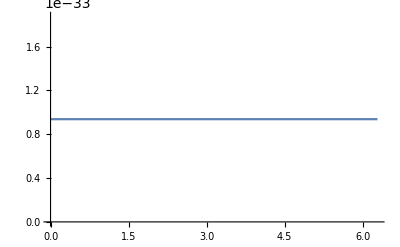

```mathematica
Plot[-1/2 √3 Sin[π]+1/4(Cos[π/2])^2,{t,0,2π}]
```

```mathematica
{1,0,0,0,0,0,0,0}//MatrixForm
```

(1
0
0
0
0
0
0
0)

```mathematica
Subscript[σ, 0]⊗Subscript[Spin, 3/2,"z"]//MatrixForm
```

```mathematica
Subscript[Spin, 3/2,"z"]⊗Subscript[Spin, 1/2,"z"]//MatrixForm
```

(3/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/4)